## Jackson 7.22

### Part a.

The imaginary part of ϵ/ϵ_0 for this problem is given by

```mathematica
(Imϵ[ω_] = λ(HeavisideTheta[ω-ω1] - HeavisideTheta[ω-ω2])) //TraditionalForm
```

λ (ω-ω1-ω-ω2)

Define some assumptions before we do the integral

```mathematica
$Assumptions = ω ∈ Reals && λ ∈ Reals && ω1 ∈ Reals && ω2 ∈ Reals && ω1 >0 && ω2 >0 && ω ≥ ω2 && ω1 < ω2;
```

The Kramers-Kronig relation given by Jackson 7.120 is

```mathematica
(Reϵ = 1 + 2/π Integrate[(ω0 Imϵ[ω0])/(ω0^2-ω^2),{ω0,0,Infinity}, PrincipalValue->True]//FullSimplify)//TraditionalForm
```

(λ log((ω^2-ω2^2)/(ω^2-ω1^2)))/π+1

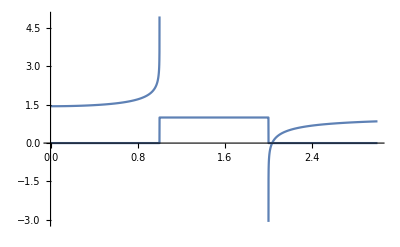

```mathematica
Plot[{Imϵ[ω],Reϵ} /. ω1 -> 1 /. ω2-> 2/. λ-> 1,{ω,0,3}]
```

### Part b.

The imaginary part of ϵ/ϵ_0 for this problem is given by

```mathematica
(Imϵ[ω_] = (λ γ ω)/((ω1^2-ω^2)^2+γ^2 ω^2)) //TraditionalForm;
```

Define some assumptions

```mathematica
$Assumptions = ω ∈ Reals && λ ∈ Reals && γ ∈ Reals && ω1 ∈ Reals && ω1 > 0 && γ > 2 ω1 && ω > 0;
```

Perform partial-fraction decomposition to perform the integral

```mathematica
(integrand = Apart[Factor[(ω0 Imϵ[ω0])/(ω0^2-ω^2),Extension->I]])//TraditionalForm
```

(ⅈ λ ω0)/(2 (ω0^2-ω^2) (ⅈ γ ω0-ω0^2+ω1^2))-(ⅈ λ ω0)/(2 (ω0^2-ω^2) (-ⅈ γ ω0-ω0^2+ω1^2))

The Kramers-Kronig relation given by Jackson 7.120 is

```mathematica
(Reϵ = 1 + 2/π Integrate[integrand,{ω0,0,Infinity}, PrincipalValue->True]/. ω1-> ω0//FullSimplify)//TraditionalForm
```

(λ (ω0^2-ω^2))/(γ^2 ω^2+(ω^2-ω0^2)^2)+1

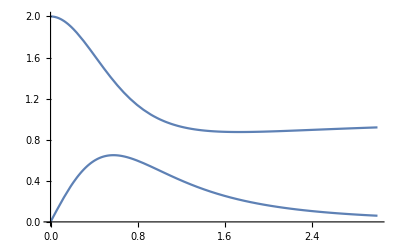

```mathematica
Plot[{Imϵ[ω],Reϵ} /. ω0 -> 1 /. ω1 -> 1 /. γ-> 2/. λ-> 1,{ω,0,3}]
```